Here is the full model we are analyzing.

```mathematica
dTh1=b1+(c1 P)/(C1+P)+(s1 Th1^2)/(S1^2+Th1^2) I12/(I12+Th2) -m Th1;
dTh2=b2+(c2 P)/(C2+P)+(s2 Th2^2)/(S2^2+Th2^2) I21/(I21+Th1)-m Th2;
dP=bp P(1-P/Kp)-a P Th2;
```

I want to create a nondimensionalized version of this model, along the lines of the nondimensionalized version of the model I created earlier, so it will have the same nondimensional variables and parameters for the immunological dynamics (th_i = Th_i/S_i, τ = t m, β_i=b_i/(m S_i), σ_i=s_i/(m S_i), and ι_ij=i_ij/I_ij) plus the dimensionless parasite variable and parameters, p=P/K_p, κ_i=C_i/K_p, χ_i=c_i/(m S_i), ρ = b_p/m and α = a S_2/m.

```mathematica
dth1=Expand[that/TH1hat(dTh1/.{Th1->TH1hat th1,Th2->TH2hat th2,P->Phat p})/.{TH1hat->S1,TH2hat->S2,Phat->Kp,that->1/m}/.b1->β1 m S1/.s1->σ1 m S1/.I12->ι12 S2/.C1->κ1 Kp/.c1->χ1 m S1]//Simplify
dth2=Expand[that/TH2hat(dTh2/.{Th1->TH1hat th1,Th2->TH2hat th2,P->Phat p})/.{TH1hat->S1,TH2hat->S2,Phat->Kp,that->1/m}/.b2->β2 m S2/.s2->σ2 m S2/.I21->ι21 S1/.C2->κ2 Kp/.c2->χ2 m S2]//Simplify
dp=that/Phat(dP/.{Th1->TH1hat th1,Th2->TH2hat th2,P->Phat p})/.{TH1hat->S1,TH2hat->S2,Phat->Kp,that->1/m}/.bp->ρ m/.a->α m/S2//Expand
```

-th1+β1+(th1^2 ι12 σ1)/((1+th1^2) (th2+ι12))+(p χ1)/(p+κ1)

-th2+β2+(th2^2 ι21 σ2)/((1+th2^2) (th1+ι21))+(p χ2)/(p+κ2)

-p th2 α+p ρ-p^2 ρ

```mathematica
params={β1->b1/(m S1),β2->b2/(m S2),σ1->s1/(m S1),σ2->s2/(m S2),ι12->I12/S2,ι21->I21/S1,κ1->C1/Kp,κ2->C2/Kp,χ1->c1/(m S1),χ2->c2/(m S2),ρ->bp/m,α->(a S2)/m}/.{S1->1000,S2->1000,s1->2000,s2->2000,b1->0.1,b2->0.1,I12->10000,I21->10000,m->0.9,c1->100,c2->100,C1->50,C2->50,bp->3,Kp->300,a->0.003}
```

{β1→0.000111111,β2→0.000111111,σ1→2.22222,σ2→2.22222,ι12→10,ι21→10,κ1→1/6,κ2→1/6,χ1→0.111111,χ2→0.111111,ρ→3.33333,α→3.33333}

For this set of parameter values, there are four stable equilibria, representing an immune state with low activation and a chronic parasite, an immune state incorrectly polarized towards Th1 with a chronic parasite, a high co-activation equilibrium that almost clears the parasite, and an immune system correctly polarized towards Th2 with an acute infection.

```mathematica
pars=params;equils=Solve[{dth1==0,dth2==0,dp==0}/.pars,{th1,th2,p}];
(* Remove all negative equilibria *)
equils2=Delete[equils,Position[Table[If[NonNegative[equils[[i,1,2]]]&&NonNegative[equils[[i,2,2]]]&&NonNegative[equils[[i,3,2]]],True,False],{i,1,Length[equils]}],False]];
(* Remove all unstable equilibria *)
equils3=Delete[equils2,Position[Table[AllTrue[Negative[Re[Eigenvalues[D[{dth1,dth2,dp},{{th1,th2,p}}]/.pars/.equils2[[i]]]][[;;]]],TrueQ],{i,1,Length[equils2]}],False]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{th1→1.74767,th2→0.120665,p→0.879335},{th1→0.129609,th2→0.129609,p→0.870391},{th1→1.21747,th2→0.984702,p→0.0152976},{th1→0.000111135,th2→1.59565,p→0.}}

If you make the parasite provoke the immune response much more strongly (10x more strongly, e.g.), then the only stable equilibria represent acute infections (or an almost acute infection, anyway).

```mathematica
pars={β1->0.00011111111111111112,β2->0.00011111111111111112,σ1->2.2222222222222223,σ2->2.2222222222222223,ι12->10,ι21->10,κ1->1/6,κ2->1/6,χ1->1.11111111111111112,χ2->1.11111111111111112,ρ->3.3333333333333335,α->3.3333333333333335};
equils=Solve[{dth1==0,dth2==0,dp==0}/.pars,{th1,th2,p}];
(* Remove all negative equilibria *)
equils2=Delete[equils,Position[Table[If[NonNegative[equils[[i,1,2]]]&&NonNegative[equils[[i,2,2]]]&&NonNegative[equils[[i,3,2]]],True,False],{i,1,Length[equils]}],False]];
(* Remove all unstable equilibria *)
equils3=Delete[equils2,Position[Table[AllTrue[Negative[Re[Eigenvalues[D[{dth1,dth2,dp},{{th1,th2,p}}]/.pars/.equils2[[i]]]][[;;]]],TrueQ],{i,1,Length[equils2]}],False]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{th1→1.20315,th2→0.998777,p→0.00122318},{th1→0.000111135,th2→1.59565,p→0.}}

If you make cross-inhibition much stronger (100x stronger, e.g.), then the only stable equilibria are a low-activation equilibrium with a chronic parasite and a high Th2 equilibrium with an acute parasite.

```mathematica
pars={β1->0.00011111111111111112,β2->0.00011111111111111112,σ1->2.2222222222222223,σ2->2.2222222222222223,ι12->0.1,ι21->0.1,κ1->1/6,κ2->1/6,χ1->0.11111111111111112,χ2->0.11111111111111112,ρ->3.3333333333333335,α->3.3333333333333335};
equils=Solve[{dth1==0,dth2==0,dp==0}/.pars,{th1,th2,p}];
(* Remove all negative equilibria *)
equils2=Delete[equils,Position[Table[If[NonNegative[equils[[i,1,2]]]&&NonNegative[equils[[i,2,2]]]&&NonNegative[equils[[i,3,2]]],True,False],{i,1,Length[equils]}],False]];
(* Remove all unstable equilibria *)
equils3=Delete[equils2,Position[Table[AllTrue[Negative[Re[Eigenvalues[D[{dth1,dth2,dp},{{th1,th2,p}}]/.pars/.equils2[[i]]]][[;;]]],TrueQ],{i,1,Length[equils2]}],False]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{th1→0.105705,th2→0.105705,p→0.894295},{th1→0.000111113,th2→1.59162,p→0.}}

Across a wide range of parameter space, because cross-inhibition is soooo strong compared to self-activation, the parasite is able to reach a chronic infection because the immune system just wants to shut down.

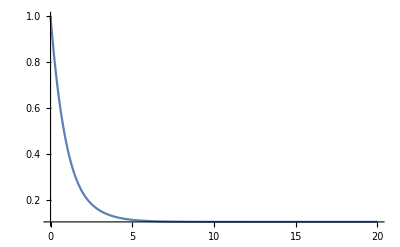

-Graphics-

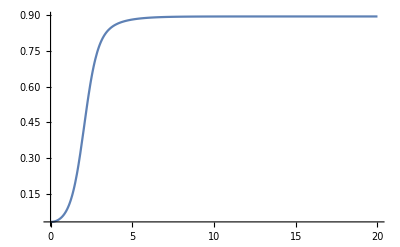

```mathematica
soln=NDSolve[{th1'[t]==(dth1/.{th1->th1[t],th2->th2[t],p->p[t]}),
th2'[t]==(dth2/.{th1->th1[t],th2->th2[t],p->p[t]}),
p'[t]==(dp/.{th1->th1[t],th2->th2[t],p->p[t]}),
th1[0]==1,th2[0]==1,p[0]==1/30}/.pars,{th1,th2,p},{t,0,100}];
Plot[th1[t]/.soln,{t,0,20},PlotRange->All]
Plot[th2[t]/.soln,{t,0,20},PlotRange->All]
Plot[p[t]/.soln,{t,0,20},PlotRange->All]
```

The only way to not have it shut down is for the immune system to start so strongly Th2 biased that it can’t help but go to that equilibrium.

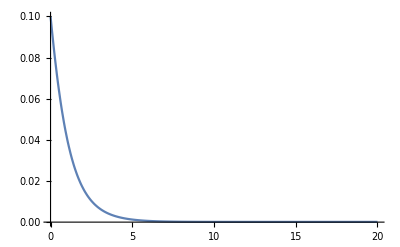

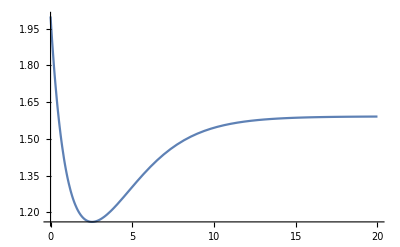

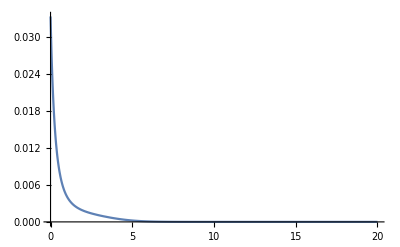

```mathematica
soln=NDSolve[{th1'[t]==(dth1/.{th1->th1[t],th2->th2[t],p->p[t]}),
th2'[t]==(dth2/.{th1->th1[t],th2->th2[t],p->p[t]}),
p'[t]==(dp/.{th1->th1[t],th2->th2[t],p->p[t]}),
th1[0]==0.1,th2[0]==2,p[0]==1/30}/.pars,{th1,th2,p},{t,0,100}];
Plot[th1[t]/.soln,{t,0,20},PlotRange->All]
Plot[th2[t]/.soln,{t,0,20},PlotRange->All]
Plot[p[t]/.soln,{t,0,20},PlotRange->All]
```

With weaker cross-inhibition, you see the emergence of a coexistence equilibrium that drives the parasite extinct, as well as the low-activation and Th1-biased equilibria where the parasite is chronic and the Th2-biased equilibrium where the parasite goes extinct.

In the absence of any self-stimulation, the system behaves like a predator-prey system and the only stable equilibrium is one with a chronic infection.

```mathematica
pars={β1->0.00011111111111111112,β2->0.00011111111111111112,σ1->0,σ2->0,ι12->100,ι21->100,κ1->1/6,κ2->1/6,χ1->0.11111111111111112,χ2->1.5*0.11111111111111112,ρ->3.3333333333333335,α->3.3333333333333335};
equils=Solve[{dth1==0,dth2==0,dp==0}/.pars,{th1,th2,p}];
(* Remove all negative equilibria *)
equils2=Delete[equils,Position[Table[If[NonNegative[equils[[i,1,2]]]&&NonNegative[equils[[i,2,2]]]&&NonNegative[equils[[i,3,2]]],True,False],{i,1,Length[equils]}],False]];
(* Remove all unstable equilibria *)
equils3=Delete[equils2,Position[Table[AllTrue[Negative[Eigenvalues[D[{dth1,dth2,dp},{{th1,th2,p}}]/.pars/.equils2[[i]]][[;;]]],TrueQ],{i,1,Length[equils2]}],False]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{th1→0.0931895,th2→0.139729,p→0.860271}}

## Parasite dynamics across parameters and initial conditions

We will first identify all of the equilibria that are stable as parameters are varied. In particular, we will vary the relative strength of cross-inhibition versus self-activation by altering the value of ι_ij: if ι_ij>1, self-activation is more sensitive to increases in the abundance of Th_i cells than cross-inhibition is to increases in Th_j cells; if ι_ij<1, the reverse is true. We also vary the relative induction of Th2 immunity versus Th1 immunity by the parasite by changing the value of χ_2 compared to χ_1.  

Identify all of the equilibria that are stable for the case where ι_ij=10 and the parasite induces Th2 much more strongly than Th1 (χ_2=4 χ_1). There is only a single equilibrium in this case, representing exclusion of the parasite.

```mathematica
pars={β1->0.00011111111111111112,β2->0.00011111111111111112,σ1->2.2222222222222223,σ2->2.2222222222222223,ι12->10,ι21->10,κ1->1/6,κ2->1/6,χ1->0.11111111111111112,χ2->4 0.11111111111111112,ρ->3.3333333333333335,α->3.3333333333333335};equils=Solve[{dth1==0,dth2==0,dp==0}/.pars,{th1,th2,p}];
(* Remove all negative equilibria *)
equils2=Delete[equils,Position[Table[If[NonNegative[equils[[i,1,2]]]&&NonNegative[equils[[i,2,2]]]&&NonNegative[equils[[i,3,2]]],True,False],{i,1,Length[equils]}],False]];
(* Remove all unstable equilibria *)
equils1040=Delete[equils2,Position[Table[AllTrue[Negative[Re[Eigenvalues[D[{dth1,dth2,dp},{{th1,th2,p}}]/.pars/.equils2[[i]]]][[;;]]],TrueQ],{i,1,Length[equils2]}],False]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{th1→0.000111135,th2→1.59565,p→0.}}

Identify all of the equilibria that are stable for the case where ι_ij=10 and the parasite induces Th2 more strongly than Th1 (χ_2=1.5 χ_1). There are now three stable equilibria, representing the two polarized responses and a high co-activation equilibrium that essentially clears the parasite.

```mathematica
pars={β1->0.00011111111111111112,β2->0.00011111111111111112,σ1->2.2222222222222223,σ2->2.2222222222222223,ι12->10,ι21->10,κ1->1/6,κ2->1/6,χ1->0.11111111111111112,χ2->1.5 0.11111111111111112,ρ->3.3333333333333335,α->3.3333333333333335};equils=Solve[{dth1==0,dth2==0,dp==0}/.pars,{th1,th2,p}];
(* Remove all negative equilibria *)
equils2=Delete[equils,Position[Table[If[NonNegative[equils[[i,1,2]]]&&NonNegative[equils[[i,2,2]]]&&NonNegative[equils[[i,3,2]]],True,False],{i,1,Length[equils]}],False]];
(* Remove all unstable equilibria *)
equils1015=Delete[equils2,Position[Table[AllTrue[Negative[Re[Eigenvalues[D[{dth1,dth2,dp},{{th1,th2,p}}]/.pars/.equils2[[i]]]][[;;]]],TrueQ],{i,1,Length[equils2]}],False]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{th1→0.000111135,th2→1.59565,p→0.},{th1→1.70651,th2→0.240866,p→0.759134},{th1→1.18578,th2→0.993191,p→0.00680884}}

Identify all of the equilibria that are stable for the case where ι_ij=10 and the parasite induces Th2 equal to Th1 (χ_2=χ_1). There are now four possible equilibria: the two polarized equilibria, a low activation equilibrium where the parasite dominates, and a high co-activation equilibrium where the parasite is almost excluded.

```mathematica
pars={β1->0.00011111111111111112,β2->0.00011111111111111112,σ1->2.2222222222222223,σ2->2.2222222222222223,ι12->10,ι21->10,κ1->1/6,κ2->1/6,χ1->0.11111111111111112,χ2->0.11111111111111112,ρ->3.3333333333333335,α->3.3333333333333335};equils=Solve[{dth1==0,dth2==0,dp==0}/.pars,{th1,th2,p}];
(* Remove all negative equilibria *)
equils2=Delete[equils,Position[Table[If[NonNegative[equils[[i,1,2]]]&&NonNegative[equils[[i,2,2]]]&&NonNegative[equils[[i,3,2]]],True,False],{i,1,Length[equils]}],False]];
(* Remove all unstable equilibria *)
equils1010=Delete[equils2,Position[Table[AllTrue[Negative[Re[Eigenvalues[D[{dth1,dth2,dp},{{th1,th2,p}}]/.pars/.equils2[[i]]]][[;;]]],TrueQ],{i,1,Length[equils2]}],False]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{th1→0.000111135,th2→1.59565,p→0.},{th1→1.74767,th2→0.120665,p→0.879335},{th1→0.129609,th2→0.129609,p→0.870391},{th1→1.21747,th2→0.984702,p→0.0152976}}

Identify all of the equilibria that are stable for the case where ι_ij=1 and the parasite induces Th2 much more strongly than Th1 (χ_2=4 χ_1). There is only a single equilibrium that is stable in this case.

```mathematica
pars={β1->0.00011111111111111112,β2->0.00011111111111111112,σ1->2.2222222222222223,σ2->2.2222222222222223,ι12->1,ι21->1,κ1->1/6,κ2->1/6,χ1->0.11111111111111112,χ2->4 0.11111111111111112,ρ->3.3333333333333335,α->3.3333333333333335};equils=Solve[{dth1==0,dth2==0,dp==0}/.pars,{th1,th2,p}];
(* Remove all negative equilibria *)
equils2=Delete[equils,Position[Table[If[NonNegative[equils[[i,1,2]]]&&NonNegative[equils[[i,2,2]]]&&NonNegative[equils[[i,3,2]]],True,False],{i,1,Length[equils]}],False]];
(* Remove all unstable equilibria *)
equils140=Delete[equils2,Position[Table[AllTrue[Negative[Re[Eigenvalues[D[{dth1,dth2,dp},{{th1,th2,p}}]/.pars/.equils2[[i]]]][[;;]]],TrueQ],{i,1,Length[equils2]}],False]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{th1→0.000111122,th2→1.59528,p→0.}}

Identify all of the equilibria that are stable for the case where ι_ij=1 and the parasite induces Th2 more strongly than Th1 (χ_2=1.5 χ_1). Again, there are three equilibria that are stable: two polarized responses but now a low immune activation equilibrium that allows the parasite to persist because the immune response self-inhibits strongly enough to allow the parasite to persist.

```mathematica
pars={β1->0.00011111111111111112,β2->0.00011111111111111112,σ1->2.2222222222222223,σ2->2.2222222222222223,ι12->1,ι21->1,κ1->1/6,κ2->1/6,χ1->0.11111111111111112,χ2->1.5 0.11111111111111112,ρ->3.3333333333333335,α->3.3333333333333335};equils=Solve[{dth1==0,dth2==0,dp==0}/.pars,{th1,th2,p}];
(* Remove all negative equilibria *)
equils2=Delete[equils,Position[Table[If[NonNegative[equils[[i,1,2]]]&&NonNegative[equils[[i,2,2]]]&&NonNegative[equils[[i,3,2]]],True,False],{i,1,Length[equils]}],False]];
(* Remove all unstable equilibria *)
equils115=Delete[equils2,Position[Table[AllTrue[Negative[Re[Eigenvalues[D[{dth1,dth2,dp},{{th1,th2,p}}]/.pars/.equils2[[i]]]][[;;]]],TrueQ],{i,1,Length[equils2]}],False]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{th1→0.000111122,th2→1.59528,p→0.},{th1→1.27075,th2→0.164977,p→0.835023},{th1→0.110592,th2→0.297957,p→0.702043}}

Identify all of the equilibria that are stable for the case where ι_ij=1 and the parasite induces Th2 equally to Th1 (χ_2=χ_1). There are three equilibria in this case; the two polarized equilibria and the low activation equilibrium.

```mathematica
pars={β1->0.00011111111111111112,β2->0.00011111111111111112,σ1->2.2222222222222223,σ2->2.2222222222222223,ι12->1,ι21->1,κ1->1/6,κ2->1/6,χ1->0.11111111111111112,χ2->0.11111111111111112,ρ->3.3333333333333335,α->3.3333333333333335};equils=Solve[{dth1==0,dth2==0,dp==0}/.pars,{th1,th2,p}];
(* Remove all negative equilibria *)
equils2=Delete[equils,Position[Table[If[NonNegative[equils[[i,1,2]]]&&NonNegative[equils[[i,2,2]]]&&NonNegative[equils[[i,3,2]]],True,False],{i,1,Length[equils]}],False]];
(* Remove all unstable equilibria *)
equils110=Delete[equils2,Position[Table[AllTrue[Negative[Re[Eigenvalues[D[{dth1,dth2,dp},{{th1,th2,p}}]/.pars/.equils2[[i]]]][[;;]]],TrueQ],{i,1,Length[equils2]}],False]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{th1→0.000111122,th2→1.59528,p→0.},{th1→1.47186,th2→0.103299,p→0.896701},{th1→0.122947,th2→0.122947,p→0.877053}}

Identify all of the equilibria that are stable for the case where ι_ij=0.1 and the parasite induces Th2 much more strongly than Th1 (χ_2=4 χ_1). There are two equilibria in this case; one where the parasite goes extinct and one where it hangs by stimulating just enough Th1 to keep Th2 from reaching the level needed to exclude the parasite.

```mathematica
pars={β1->0.00011111111111111112,β2->0.00011111111111111112,σ1->2.2222222222222223,σ2->2.2222222222222223,ι12->0.1,ι21->0.1,κ1->1/6,κ2->1/6,χ1->0.11111111111111112,χ2->4 0.11111111111111112,ρ->3.3333333333333335,α->3.3333333333333335};equils=Solve[{dth1==0,dth2==0,dp==0}/.pars,{th1,th2,p}];
(* Remove all negative equilibria *)
equils2=Delete[equils,Position[Table[If[NonNegative[equils[[i,1,2]]]&&NonNegative[equils[[i,2,2]]]&&NonNegative[equils[[i,3,2]]],True,False],{i,1,Length[equils]}],False]];
(* Remove all unstable equilibria *)
equils0140=Delete[equils2,Position[Table[AllTrue[Negative[Re[Eigenvalues[D[{dth1,dth2,dp},{{th1,th2,p}}]/.pars/.equils2[[i]]]][[;;]]],TrueQ],{i,1,Length[equils2]}],False]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{th1→0.000111113,th2→1.59162,p→0.},{th1→0.0704507,th2→0.726786,p→0.273214}}

Identify all of the equilibria that are stable for the case where ι_ij=0.1 and the parasite induces Th2 more strongly than Th1 (χ_2=2 χ_1). There are two equilibria in this case; one where the parasite goes extinct and one where it becomes chronic because the immune response is trapped at low activation.

```mathematica
pars={β1->0.00011111111111111112,β2->0.00011111111111111112,σ1->2.2222222222222223,σ2->2.2222222222222223,ι12->0.1,ι21->0.1,κ1->1/6,κ2->1/6,χ1->0.11111111111111112,χ2->1.5 0.11111111111111112,ρ->3.3333333333333335,α->3.3333333333333335};equils=Solve[{dth1==0,dth2==0,dp==0}/.pars,{th1,th2,p}];
(* Remove all negative equilibria *)
equils2=Delete[equils,Position[Table[If[NonNegative[equils[[i,1,2]]]&&NonNegative[equils[[i,2,2]]]&&NonNegative[equils[[i,3,2]]],True,False],{i,1,Length[equils]}],False]];
(* Remove all unstable equilibria *)
equils0115=Delete[equils2,Position[Table[AllTrue[Negative[Re[Eigenvalues[D[{dth1,dth2,dp},{{th1,th2,p}}]/.pars/.equils2[[i]]]][[;;]]],TrueQ],{i,1,Length[equils2]}],False]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{th1→0.000111113,th2→1.59162,p→0.},{th1→0.100946,th2→0.169954,p→0.830046}}

Identify all of the equilibria that are stable for the case where ι_ij=0.1 and the parasite induces Th2 equally to Th1 (χ_2=χ_1). There are two equilibria in this case; one where the parasite goes extinct and one where it becomes chronic because immune activation remains low - it does not, however, drive polarization of the immune response towards Th1.

```mathematica
pars={β1->0.00011111111111111112,β2->0.00011111111111111112,σ1->2.2222222222222223,σ2->2.2222222222222223,ι12->0.1,ι21->0.1,κ1->1/6,κ2->1/6,χ1->0.11111111111111112,χ2->0.11111111111111112,ρ->3.3333333333333335,α->3.3333333333333335};equils=Solve[{dth1==0,dth2==0,dp==0}/.pars,{th1,th2,p}];
(* Remove all negative equilibria *)
equils2=Delete[equils,Position[Table[If[NonNegative[equils[[i,1,2]]]&&NonNegative[equils[[i,2,2]]]&&NonNegative[equils[[i,3,2]]],True,False],{i,1,Length[equils]}],False]];
(* Remove all unstable equilibria *)
equils0110=Delete[equils2,Position[Table[AllTrue[Negative[Re[Eigenvalues[D[{dth1,dth2,dp},{{th1,th2,p}}]/.pars/.equils2[[i]]]][[;;]]],TrueQ],{i,1,Length[equils2]}],False]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{th1→0.000111113,th2→1.59162,p→0.},{th1→0.105705,th2→0.105705,p→0.894295}}

Okay, there are some important takeaways here. First, only when self-activation is more sensitive than cross-inhibition is false polarization possible. When cross-inhibition is more sensitive than self-activation, even when the parasite induction is equal the only possibilities are polarization or an immune response that is trapped in a low activation state. It is not possible for the parasite to drive immune polarization towards Th1.

```mathematica
Sort[DeleteDuplicates[Round[Join[{equils1040[[1,3,2]]},
equils1015[[;;,3,2]],
equils1010[[;;,3,2]],
{equils140[[1,3,2]]},
equils115[[;;,3,2]],
equils110[[;;,3,2]],
equils0140[[;;,3,2]],
equils0115[[;;,3,2]],
equils0110[[;;,3,2]]
],0.001]]]
```

{0.,0.007,0.015,0.273,0.702,0.759,0.83,0.835,0.87,0.877,0.879,0.894,0.897}

```mathematica
equils1040
equils1015
equils1010
equils140
equils115
equils110
equils0140
equils0115
equils0110
```

{{th1→0.000111135,th2→1.59565,p→0.}}

{{th1→0.000111135,th2→1.59565,p→0.},{th1→1.70651,th2→0.240866,p→0.759134},{th1→1.18578,th2→0.993191,p→0.00680884}}

{{th1→0.000111135,th2→1.59565,p→0.},{th1→1.74767,th2→0.120665,p→0.879335},{th1→0.129609,th2→0.129609,p→0.870391},{th1→1.21747,th2→0.984702,p→0.0152976}}

{{th1→0.000111122,th2→1.59528,p→0.}}

{{th1→0.000111122,th2→1.59528,p→0.},{th1→1.27075,th2→0.164977,p→0.835023},{th1→0.110592,th2→0.297957,p→0.702043}}

{{th1→0.000111122,th2→1.59528,p→0.},{th1→1.47186,th2→0.103299,p→0.896701},{th1→0.122947,th2→0.122947,p→0.877053}}

{{th1→0.000111113,th2→1.59162,p→0.},{th1→0.0704507,th2→0.726786,p→0.273214}}

{{th1→0.000111113,th2→1.59162,p→0.},{th1→0.100946,th2→0.169954,p→0.830046}}

{{th1→0.000111113,th2→1.59162,p→0.},{th1→0.105705,th2→0.105705,p→0.894295}}

```mathematica
Round[{{equils1040[[1,3,2]]},
equils1015[[;;,3,2]],
equils1010[[;;,3,2]],
{equils140[[1,3,2]]},
equils115[[;;,3,2]],
equils110[[;;,3,2]],
equils0140[[;;,3,2]],
equils0115[[;;,3,2]],
equils0110[[;;,3,2]]},0.001]
```

{{0.},{0.,0.759,0.007},{0.,0.879,0.87,0.015},{0.},{0.,0.835,0.702},{0.,0.897,0.877},{0.,0.273},{0.,0.83},{0.,0.894}}

```mathematica
pars={β1->0.00011111111111111112,β2->0.00011111111111111112,σ1->2.2222222222222223,σ2->2.2222222222222223,ι12->10,ι21->10,κ1->1/6,κ2->1/6,χ1->0.4.11111111111111112`,χ2->1.6 0.11111111111111112,ρ->3.3333333333333335,α->3.3333333333333335};equils=Solve[{dth1==0,dth2==0,dp==0}/.pars,{th1,th2,p}];
(* Remove all negative equilibria *)
equils2=Delete[equils,Position[Table[If[NonNegative[equils[[i,1,2]]]&&NonNegative[equils[[i,2,2]]]&&NonNegative[equils[[i,3,2]]],True,False],{i,1,Length[equils]}],False]];
(* Remove all unstable equilibria *)
equils0110=Delete[equils2,Position[Table[AllTrue[Negative[Re[Eigenvalues[D[{dth1,dth2,dp},{{th1,th2,p}}]/.pars/.equils2[[i]]]][[;;]]],TrueQ],{i,1,Length[equils2]}],False]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{th1→0.000111135,th2→1.59565,p→0.}}

```mathematica
pars={β1->0.00011111111111111112,β2->0.00011111111111111112,σ1->2.2222222222222223,σ2->2.2222222222222223,ι12->10,ι21->10,κ1->1/6,κ2->1/6,χ1->0.5.11111111111111112`,χ2->1.5 0.11111111111111112,ρ->3.3333333333333335,α->3.3333333333333335};equils=Solve[{dth1==0,dth2==0,dp==0}/.pars,{th1,th2,p}];
(* Remove all negative equilibria *)
equils2=Delete[equils,Position[Table[If[NonNegative[equils[[i,1,2]]]&&NonNegative[equils[[i,2,2]]]&&NonNegative[equils[[i,3,2]]],True,False],{i,1,Length[equils]}],False]]
Table[Eigenvalues[D[{dth1,dth2,dp},{{th1,th2,p}}]/.pars/.equils2[[i]]],{i,1,Length[equils2]}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{th1→0.000111135,th2→1.59565,p→0.},{th1→0.000111137,th2→0.62655,p→0.},{th1→0.000111139,th2→0.000111139,p→0.},{th1→0.62655,th2→0.000111137,p→0.},{th1→0.780726,th2→0.780726,p→0.},{th1→1.07968,th2→1.07968,p→0.},{th1→1.59565,th2→0.000111135,p→0.},{th1→1.61184,th2→0.245038,p→0.754962},{th1→1.54271,th2→0.433894,p→0.566106},{th1→1.16821,th2→0.994858,p→0.00514235}}

{{-1.98549,-0.999574,-0.436038},{1.24483,-0.999535,0.435944},{3.33296,-0.999506,-0.999506},{3.33296,-0.999535,0.435944},{0.730914,0.314828,0.170011},{-0.265597,-0.174046,0.0208277},{3.33296,-0.999574,-0.436038},{-2.48093,-0.465836,-0.195},{-1.83836,-0.43278,0.142569},{-0.178681+0. ⅈ,0.00301318+0.102281 ⅈ,0.00301318-0.102281 ⅈ}}

```mathematica
pars={β1->0.00011111111111111112,β2->0.00011111111111111112,σ1->2.2222222222222223,σ2->2.2222222222222223,ι12->10,ι21->10,κ1->1/6,κ2->1/6,χ1->0.6.11111111111111112`,χ2->1.4 0.11111111111111112,ρ->3.3333333333333335,α->3.3333333333333335};equils=Solve[{dth1==0,dth2==0,dp==0}/.pars,{th1,th2,p}];
(* Remove all negative equilibria *)
equils2=Delete[equils,Position[Table[If[NonNegative[equils[[i,1,2]]]&&NonNegative[equils[[i,2,2]]]&&NonNegative[equils[[i,3,2]]],True,False],{i,1,Length[equils]}],False]]
Table[Eigenvalues[D[{dth1,dth2,dp},{{th1,th2,p}}]/.pars/.equils2[[i]]],{i,1,Length[equils2]}]
Delete[equils2,Position[Table[AllTrue[Negative[Re[Eigenvalues[D[{dth1,dth2,dp},{{th1,th2,p}}]/.pars/.equils2[[i]]]][[;;]]],TrueQ],{i,1,Length[equils2]}],False]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{th1→0.000111135,th2→1.59565,p→0.},{th1→0.000111137,th2→0.62655,p→0.},{th1→0.000111139,th2→0.000111139,p→0.},{th1→0.62655,th2→0.000111137,p→0.},{th1→0.780726,th2→0.780726,p→0.},{th1→1.07968,th2→1.07968,p→0.},{th1→1.59565,th2→0.000111135,p→0.},{th1→1.6447,th2→0.207207,p→0.792793},{th1→0.533147,th2→0.272631,p→0.727369},{th1→0.537934,th2→0.303696,p→0.696304},{th1→1.54141,th2→0.489165,p→0.510835},{th1→1.17294,th2→0.993998,p→0.00600241}}

{{-1.98549,-0.999574,-0.436038},{1.24483,-0.999535,0.435944},{3.33296,-0.999506,-0.999506},{3.33296,-0.999535,0.435944},{0.730914,0.314828,0.170011},{-0.265597,-0.174046,0.0208277},{3.33296,-0.999574,-0.436038},{-2.61076,-0.484796,-0.298325},{-2.39156,0.400457,-0.0381898},{-2.28668,0.398559,0.0364984},{-1.65087,-0.436523,0.184191},{-0.178098+0. ⅈ,-0.000696429+0.104172 ⅈ,-0.000696429-0.104172 ⅈ}}

{{th1→0.000111135,th2→1.59565,p→0.},{th1→1.6447,th2→0.207207,p→0.792793},{th1→1.17294,th2→0.993998,p→0.00600241}}

```mathematica
1.3/0.7
```

1.85714

```mathematica
pars={β1->0.00011111111111111112,β2->0.00011111111111111112,σ1->2.2222222222222223,σ2->2.2222222222222223,ι12->10,ι21->10,κ1->1/6,κ2->1/6,χ1->0.5.11111111111111112`,χ2->1.5 0.11111111111111112,ρ->3.3333333333333335,α->3.3333333333333335};equils=Solve[{dth1==0,dth2==0,dp==0}/.pars,{th1,th2,p}];
(* Remove all negative equilibria *)
equils2=Delete[equils,Position[Table[If[NonNegative[equils[[i,1,2]]]&&NonNegative[equils[[i,2,2]]]&&NonNegative[equils[[i,3,2]]],True,False],{i,1,Length[equils]}],False]]
Table[Eigenvalues[D[{dth1,dth2,dp},{{th1,th2,p}}]/.pars/.equils2[[i]]],{i,1,Length[equils2]}]
Delete[equils2,Position[Table[AllTrue[Negative[Re[Eigenvalues[D[{dth1,dth2,dp},{{th1,th2,p}}]/.pars/.equils2[[i]]]][[;;]]],TrueQ],{i,1,Length[equils2]}],False]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{th1→0.000111135,th2→1.59565,p→0.},{th1→0.000111137,th2→0.62655,p→0.},{th1→0.000111139,th2→0.000111139,p→0.},{th1→0.62655,th2→0.000111137,p→0.},{th1→0.780726,th2→0.780726,p→0.},{th1→1.07968,th2→1.07968,p→0.},{th1→1.59565,th2→0.000111135,p→0.},{th1→1.61184,th2→0.245038,p→0.754962},{th1→1.54271,th2→0.433894,p→0.566106},{th1→1.16821,th2→0.994858,p→0.00514235}}

{{-1.98549,-0.999574,-0.436038},{1.24483,-0.999535,0.435944},{3.33296,-0.999506,-0.999506},{3.33296,-0.999535,0.435944},{0.730914,0.314828,0.170011},{-0.265597,-0.174046,0.0208277},{3.33296,-0.999574,-0.436038},{-2.48093,-0.465836,-0.195},{-1.83836,-0.43278,0.142569},{-0.178681+0. ⅈ,0.00301318+0.102281 ⅈ,0.00301318-0.102281 ⅈ}}

{{th1→0.000111135,th2→1.59565,p→0.},{th1→1.61184,th2→0.245038,p→0.754962}}

```mathematica
pars={β1->0.00011111111111111112,β2->0.00011111111111111112,σ1->2.2222222222222223,σ2->2.2222222222222223,ι12->10,ι21->10,κ1->1/6,κ2->1/6,χ1->0.5.11111111111111112`,χ2->1.5 0.11111111111111112,ρ->3.3333333333333335,α->3.3333333333333335};equils=Solve[{dth1==0,dth2==0,dp==0}/.pars,{th1,th2,p}];
(* Remove all negative equilibria *)
equils2=Delete[equils,Position[Table[If[NonNegative[equils[[i,1,2]]]&&NonNegative[equils[[i,2,2]]]&&NonNegative[equils[[i,3,2]]],True,False],{i,1,Length[equils]}],False]]
Table[Eigenvalues[D[{dth1,dth2,dp},{{th1,th2,p}}]/.pars/.equils2[[i]]],{i,1,Length[equils2]}]
Delete[equils2,Position[Table[AllTrue[Negative[Re[Eigenvalues[D[{dth1,dth2,dp},{{th1,th2,p}}]/.pars/.equils2[[i]]]][[;;]]],TrueQ],{i,1,Length[equils2]}],False]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{th1→0.000111135,th2→1.59565,p→0.},{th1→0.000111137,th2→0.62655,p→0.},{th1→0.000111139,th2→0.000111139,p→0.},{th1→0.62655,th2→0.000111137,p→0.},{th1→0.780726,th2→0.780726,p→0.},{th1→1.07968,th2→1.07968,p→0.},{th1→1.59565,th2→0.000111135,p→0.},{th1→1.16453,th2→0.995512,p→0.00448812}}

{{-1.98549,-0.999574,-0.436038},{1.24483,-0.999535,0.435944},{3.33296,-0.999506,-0.999506},{3.33296,-0.999535,0.435944},{0.730914,0.314828,0.170011},{-0.265597,-0.174046,0.0208277},{3.33296,-0.999574,-0.436038},{-0.179176+0. ⅈ,0.00591017+0.100772 ⅈ,0.00591017-0.100772 ⅈ}}

{{th1→0.000111135,th2→1.59565,p→0.}}

```mathematica
pars={β1->0.00011111111111111112,β2->0.00011111111111111112,σ1->2.2222222222222223,σ2->2.2222222222222223,ι12->0.1,ι21->0.1,κ1->1/6,κ2->1/6,χ1->0.5.11111111111111112`,χ2->1.5 0.11111111111111112,ρ->3.3333333333333335,α->3.3333333333333335};equils=Solve[{dth1==0,dth2==0,dp==0}/.pars,{th1,th2,p}];
(* Remove all negative equilibria *)
equils2=Delete[equils,Position[Table[If[NonNegative[equils[[i,1,2]]]&&NonNegative[equils[[i,2,2]]]&&NonNegative[equils[[i,3,2]]],True,False],{i,1,Length[equils]}],False]]
Table[Eigenvalues[D[{dth1,dth2,dp},{{th1,th2,p}}]/.pars/.equils2[[i]]],{i,1,Length[equils2]}]
Delete[equils2,Position[Table[AllTrue[Negative[Re[Eigenvalues[D[{dth1,dth2,dp},{{th1,th2,p}}]/.pars/.equils2[[i]]]][[;;]]],TrueQ],{i,1,Length[equils2]}],False]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{th1→0.000111113,th2→1.59162,p→0.},{th1→0.000111115,th2→0.628136,p→0.},{th1→0.000111139,th2→0.000111139,p→0.},{th1→0.628136,th2→0.000111115,p→0.},{th1→1.59162,th2→0.000111113,p→0.},{th1→0.0479202,th2→0.191372,p→0.808628},{th1→0.0173079,th2→0.925689,p→0.0743113}}

{{-1.97207,-0.999971,-0.433989},{1.23955,-0.999932,0.433896},{3.33296,-0.999507,-0.999506},{3.33296,-0.999932,0.433896},{3.33296,-0.999971,-0.433989},{-2.65701,-0.94456,-0.486003},{-0.73799+0.413847 ⅈ,-0.73799-0.413847 ⅈ,0.252907+0. ⅈ}}

{{th1→0.000111113,th2→1.59162,p→0.},{th1→0.0479202,th2→0.191372,p→0.808628}}

Stable equilibria for different relative inductions:

```mathematica
Table[pars={β1->0.00011111111111111112,β2->0.00011111111111111112,σ1->2.2222222222222223,σ2->2.2222222222222223,ι12->10,ι21->10,κ1->1/6,κ2->1/6,χ1->(1-rel) 0.11111111111111112,χ2->(1+rel)  0.11111111111111112,ρ->3.3333333333333335,α->3.3333333333333335};equils=Solve[{dth1==0,dth2==0,dp==0}/.pars,{th1,th2,p}];
(* Remove all negative equilibria *)
equils2=Delete[equils,Position[Table[If[NonNegative[equils[[i,1,2]]]&&NonNegative[equils[[i,2,2]]]&&NonNegative[equils[[i,3,2]]],True,False],{i,1,Length[equils]}],False]];
Table[Eigenvalues[D[{dth1,dth2,dp},{{th1,th2,p}}]/.pars/.equils2[[i]]],{i,1,Length[equils2]}];
Delete[equils2,Position[Table[AllTrue[Negative[Re[Eigenvalues[D[{dth1,dth2,dp},{{th1,th2,p}}]/.pars/.equils2[[i]]]][[;;]]],TrueQ],{i,1,Length[equils2]}],False]],{rel,0,0.5,0.1}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{{{th1→0.000111135,th2→1.59565,p→0.},{th1→1.74767,th2→0.120665,p→0.879335},{th1→0.129609,th2→0.129609,p→0.870391},{th1→1.21747,th2→0.984702,p→0.0152976}},{{th1→0.000111135,th2→1.59565,p→0.},{th1→1.72413,th2→0.137908,p→0.862092},{th1→0.109736,th2→0.151726,p→0.848274},{th1→1.19975,th2→0.988674,p→0.0113256}},{{th1→0.000111135,th2→1.59565,p→0.},{th1→1.69944,th2→0.157282,p→0.842718},{th1→0.0925047,th2→0.180083,p→0.819917},{th1→1.1877,th2→0.991164,p→0.0088364}},{{th1→0.000111135,th2→1.59565,p→0.},{th1→1.67322,th2→0.179739,p→0.820261},{th1→0.0768513,th2→0.227023,p→0.772977},{th1→1.17919,th2→0.992827,p→0.0071732}},{{th1→0.000111135,th2→1.59565,p→0.},{th1→1.6447,th2→0.207207,p→0.792793},{th1→1.17294,th2→0.993998,p→0.00600241}},{{th1→0.000111135,th2→1.59565,p→0.},{th1→1.61184,th2→0.245038,p→0.754962}}}

```mathematica
pars={β1->0.00011111111,β2->0.0001111111,σ1->2.2222222222222223,σ2->2.2222222222222223,ι12->10,ι21->10,κ1->1/6,κ2->1/6,χ1->(1-0.5) 0.111111,χ2->(1+0.5)  0.111111,ρ->3.3333333333333335,α->3.3333333333333335};equils=Solve[{dth1==0,dth2==0,dp==0}/.pars,{th1,th2,p}];
(* Remove all negative equilibria *)
equils2=Delete[equils,Position[Table[If[NonNegative[equils[[i,1,2]]]&&NonNegative[equils[[i,2,2]]]&&NonNegative[equils[[i,3,2]]],True,False],{i,1,Length[equils]}],False]]
Table[Eigenvalues[D[{dth1,dth2,dp},{{th1,th2,p}}]/.pars/.equils2[[i]]],{i,1,Length[equils2]}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{th1→0.000111135,th2→1.59565,p→0.},{th1→0.000111137,th2→0.62655,p→0.},{th1→0.000111139,th2→0.000111139,p→0.},{th1→0.62655,th2→0.000111137,p→0.},{th1→0.780726,th2→0.780726,p→0.},{th1→1.07968,th2→1.07968,p→0.},{th1→1.59565,th2→0.000111135,p→0.},{th1→1.61184,th2→0.245037,p→0.754963},{th1→1.54271,th2→0.433895,p→0.566105},{th1→1.16821,th2→0.994858,p→0.00514236}}

{{-1.98549,-0.999574,-0.436038},{1.24483,-0.999535,0.435944},{3.33296,-0.999506,-0.999506},{3.33296,-0.999535,0.435944},{0.730914,0.314828,0.170011},{-0.265597,-0.174046,0.0208277},{3.33296,-0.999574,-0.436038},{-2.48094,-0.465836,-0.195002},{-1.83836,-0.43278,0.14257},{-0.178681+0. ⅈ,0.00301317+0.102281 ⅈ,0.00301317-0.102281 ⅈ}}

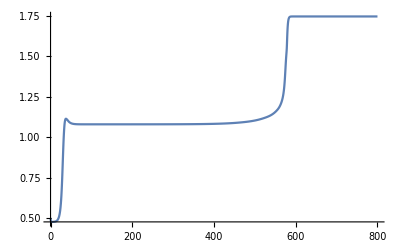

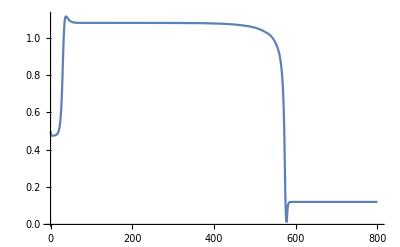

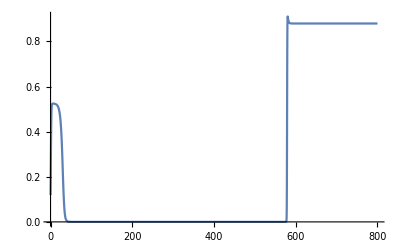

```mathematica
pars={β1->0.00011111111,β2->0.0001111111,σ1->2.2222222222222223,σ2->2.2222222222222223,ι12->10,ι21->10,κ1->1/6,κ2->1/6,χ1->(1-0) 0.111111,χ2->(1+0)  0.111111,ρ->3.3333333333333335,α->3.3333333333333335};soln=NDSolve[{th1'[t]==(dth1/.{th1->th1[t],th2->th2[t],p->p[t]}),
th2'[t]==(dth2/.{th1->th1[t],th2->th2[t],p->p[t]}),
p'[t]==(dp/.{th1->th1[t],th2->th2[t],p->p[t]}),
th1[0]==0.5,th2[0]==0.5,p[0]==0.119}/.pars,{th1,th2,p},{t,0,800},Method->"StiffnessSwitching"];
Plot[th1[t]/.soln,{t,0,800},PlotRange->All]
Plot[th2[t]/.soln,{t,0,800},PlotRange->All]
Plot[p[t]/.soln,{t,0,800},PlotRange->All]
```

```mathematica
1/(24 0.0002)
```

208.333